POTW - 4a
We’re going to write code this week!  For reals! This is excerpted from the online book, check it out: www.wolfram.com/language/elementary-introduction/03-first-look-at-lists.html

3 | First Look at Lists

Lists are a basic way to collect things together in the Wolfram Language. {1,2,3} is a list of numbers. On their own, lists don’t do anything; they’re just a way to store things. So if you give a list as input, it’ll just come back unchanged:

```mathematica
{1,2,3,4,a,b,c}
```

{1,2,3,4,a,b,c}

ListPlot is a function that makes a plot of a list of numbers.

Plot the list of numbers: {1,1,2,2,3,4,4}

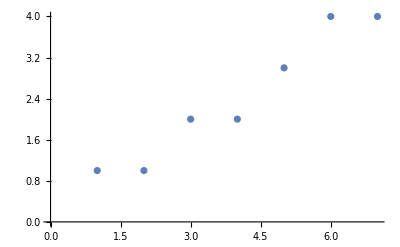

```mathematica
ListPlot[{1,1,2,2,3,4,4}]
```

Plot the list of numbers {10,9,8,7,3,2,1}

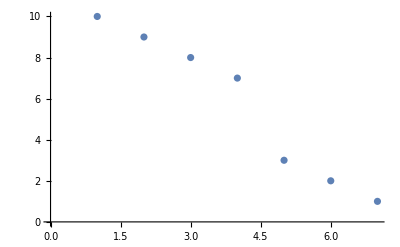

```mathematica
ListPlot[{10,9,8,7,3,2,1}]
```

Range is a function that makes a list of numbers.

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Generate a list of numbers, then plot it:

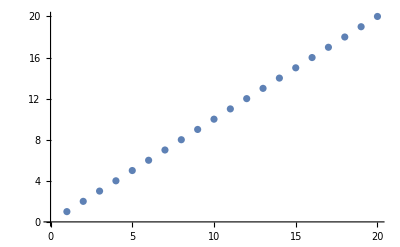

```mathematica
ListPlot[Range[20]]
```

Reverse reverses the elements in a list.

Reverse the elements in a list:

```mathematica
Reverse[{1,2,3,4}]
```

{4,3,2,1}

Reverse what Range has generated:

```mathematica
Reverse[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

Plot the reversed list:

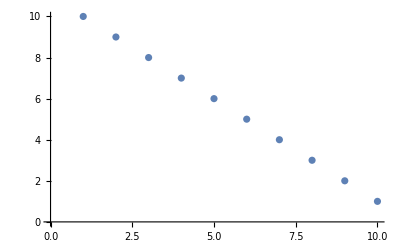

```mathematica
ListPlot[Reverse[Range[10]]]
```

Join joins lists together, making a single list as the result

Join lists together:

```mathematica
Join[{1,2,3},{4,5},{6,7}]
```

{1,2,3,4,5,6,7}

```mathematica
Join[{1,2,3},{1,2,3,4,5}]
```

{1,2,3,1,2,3,4,5}

Join two lists made by Range:

```mathematica
Join[Range[3],Range[5]]
```

{1,2,3,1,2,3,4,5}

Plot three lists joined together:

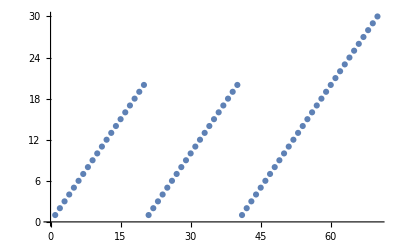

```mathematica
ListPlot[Join[Range[20],Range[20],Range[30]]]
```

Reverse the list in the middle:

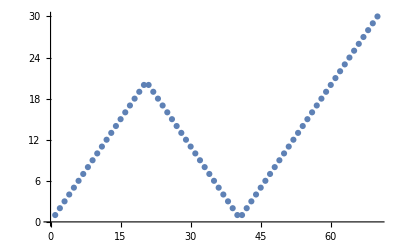

```mathematica
ListPlot[Join[Range[20],Reverse[Range[20]],Range[30]]]
```

Vocabulary

{1,2,3,4}				list of elements
ListPlot[{1,2,3,4}]		plot a list of numbers
Range[10]				range of numbers
Reverse[{1,2,3}]			reverse a list
Join[{4,5,6},{2,3,2}]		joins lists together

Exercises
Complete the following exercises by writing code.  Remember, coding is collaborative -- don’t work alone!  Get help, work together, ask questions.  You can do this!

1. Use Range to create the list {1,2,3,4}.

2. Make a list of numbers up to 100.

3. Use Range and Reverse to create {4,3,2,1}.

4. Make a list of numbers from 1 to 50 in reverse order.

5. Use Range, Reverse and Join to create {1,2,3,4,4,3,2,1}.

6. Plot a list that counts up from 1 to 100, then down to 1.

7. Use Range and RandomInteger to make a list with a random length up to 10.

8. Find a simpler form for Reverse[Reverse[Range[10]]].

9. Find a simpler form for Join[{1,2},Join[{3,4},{5}]].

10. Find a simpler form for Join[Range[10],Join[Range[10],Range[5]]].

11. Find a simpler form for Reverse[Join[Range[20],Reverse[Range[20]]]].

12. Compute the reverse of the reverse of {1,2,3,4}.

13. Use Range, Reverse and Join to create the list {1,2,3,4,5,4,3,2,1}.

14. Use Range, Reverse and Join to create {3,2,1,4,3,2,1,5,4,3,2,1}.

15. Plot the list of numbers {10,11,12,13,14}.

16. Find a simpler form for Join[Join[Range[10],Reverse[Range[10]]],Range[10]].

## Initialization

This is stuff that we put in the document.  This code runs as you open the document.  Feel free to mess with it.

```mathematica
Clear[x]
Clear[f]
Clear[g]
Clear[h]
SetOptions[EvaluationNotebook[], Background->Interpreter["Color"]["RGB 250 250 250"]]
```